```mathematica
Transpose[{{1,3,5,7,9},{2,4,6,8,10}}]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

```mathematica
Grid[{{1,3,5,7,9},{2,4,6,8,10}}]
```

1 | 3 | 5 | 7 | 9
2 | 4 | 6 | 8 | 10

```mathematica
Grid[{{1,2},{3,4},{5,6},{7,8},{9,10}}] (*Transpuesta*)
```

1 | 2
3 | 4
5 | 6
7 | 8
9 | 10

```mathematica
Thread[{1,2,3,4,5}->{2,3,4,5,1}]
```

```mathematica
{1->2,2->3,3->4,4->5,5->4}
```

```mathematica
{1->2,2->3,3->4,4->5,5->3}
```

{1→2,2→3,3→4,4→5,5→3}

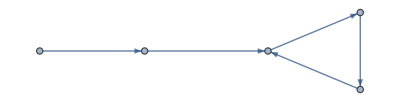

```mathematica
Graph[%]
```

```mathematica
Grid[Partition[Range[12],3],Frame->All]
```

1 | 2 | 3
4 | 5 | 6
7 | 8 | 9
10 | 11 | 12

```mathematica
NestList[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},2]
```

{{{1}},{{1,0},{1,1}},{{1,0,0,0},{1,1,0,0},{1,0,1,0},{1,1,1,1}}}

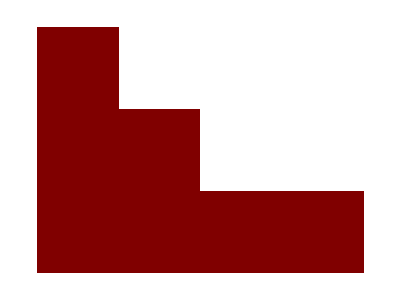

```mathematica
ArrayPlot[%]
```


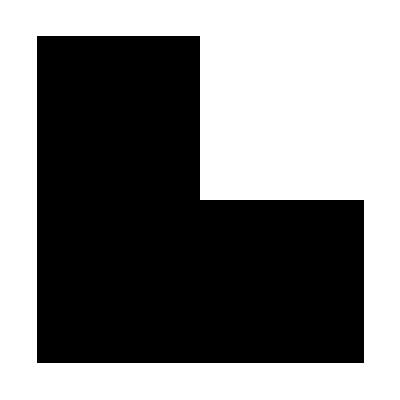
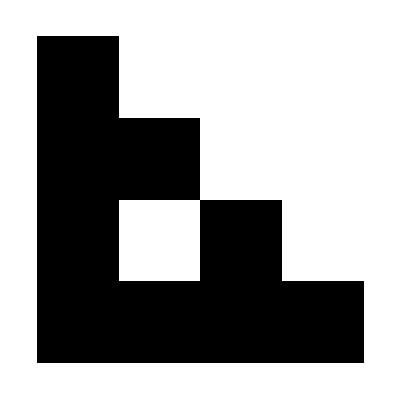
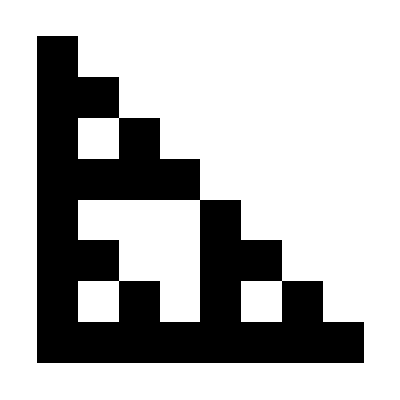
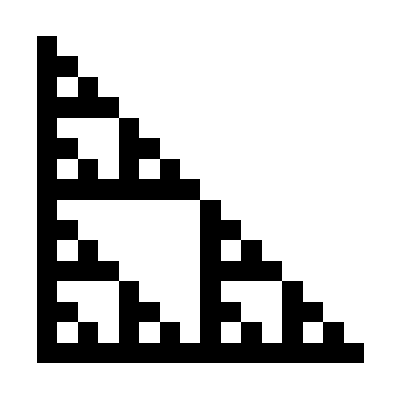
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@NestList[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},6]
```

```mathematica
Split[{1,1,1,2,2,1,1,3,1,1,1,2}]
```

{{1,1,1},{2,2},{1,1},{3},{1,1,1},{2}}

```mathematica
Gather[{1,1,1,2,2,1,1,3,1,1,1,2}]
```

{{1,1,1,1,1,1,1,1},{2,2,2},{3}}

```mathematica
GatherBy[Characters["It's true that 2+2 is equal to 4!"],LetterQ]
```

{{I,t,s,t,r,u,e,t,h,a,t,i,s,e,q,u,a,l,t,o},{', , , ,2,+,2, , , , ,4,!}}

```mathematica
Sort[Table[IntegerDigits[2^n],{n,10}]]
```

{{2},{4},{8},{1,6},{3,2},{6,4},{1,2,8},{2,5,6},{5,1,2},{1,0,2,4}}

```mathematica
SortBy[Table[IntegerDigits[2^n],{n,10}],Last]
```

{{2},{3,2},{5,1,2},{4},{6,4},{1,0,2,4},{1,6},{2,5,6},{8},{1,2,8}}

```mathematica
Union[Alphabet["English"],Alphabet["Swedish"],Alphabet["Turkish"]]
```

{ğ,ş,a,å,ä,b,c,ç,d,e,f,g,h,i,ı,j,k,l,m,n,o,ö,p,q,r,s,t,u,ü,v,w,x,y,z}

```mathematica
Complement[Alphabet["Swedish"],Alphabet["English"]]
```

{å,ä,ö}

```mathematica
Tuples[{Red,Blue,Green},3]
```

{{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]},{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0]},{RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},{RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 1, 0]},{RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[1, 0, 0]},{RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 0]},{RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]}}

```mathematica
Thread[Alphabet[]-> Range[26]]
```

{a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,o→15,p→16,q→17,r→18,s→19,t→20,u→21,v→22,w→23,x→24,y→25,z→26}

```mathematica
Grid[Partition[Take[Characters[WikipediaData["computers"]],400],20],Frame-> All]
```

A |   | c | o | m | p | u | t | e | r |   | i | s |   | a |   | m | a | c | h
i | n | e |   | t | h | a | t |   | c | a | n |   | b | e |   | i | n | s | t
r | u | c | t | e | d |   | t | o |   | c | a | r | r | y |   | o | u | t |  
s | e | q | u | e | n | c | e | s |   | o | f |   | a | r | i | t | h | m | e
t | i | c |   | o | r |   | l | o | g | i | c | a | l |   | o | p | e | r | a
t | i | o | n | s |   | a | u | t | o | m | a | t | i | c | a | l | l | y |  
v | i | a |   | c | o | m | p | u | t | e | r |   | p | r | o | g | r | a | m
m | i | n | g | . |   | M | o | d | e | r | n |   | c | o | m | p | u | t | e
r | s |   | h | a | v | e |   | t | h | e |   | a | b | i | l | i | t | y |  
t | o |   | f | o | l | l | o | w |   | g | e | n | e | r | a | l | i | z | e
d |   | s | e | t | s |   | o | f |   | o | p | e | r | a | t | i | o | n | s
, |   | c | a | l | l | e | d |   | p | r | o | g | r | a | m | s | . |   | T
h | e | s | e |   | p | r | o | g | r | a | m | s |   | e | n | a | b | l | e
  | c | o | m | p | u | t | e | r | s |   | t | o |   | p | e | r | f | o | r
m |   | a | n |   | e | x | t | r | e | m | e | l | y |   | w | i | d | e |  
r | a | n | g | e |   | o | f |   | t | a | s | k | s | . |   | A |   | " | c
o | m | p | l | e | t | e | " |   | c | o | m | p | u | t | e | r |   | i | n
c | l | u | d | i | n | g |   | t | h | e |   | h | a | r | d | w | a | r | e
, |   | t | h | e |   | o | p | e | r | a | t | i | n | g |   | s | y | s | t
e | m |   | ( | m | a | i | n |   | s | o | f | t | w | a | r | e | ) | , |

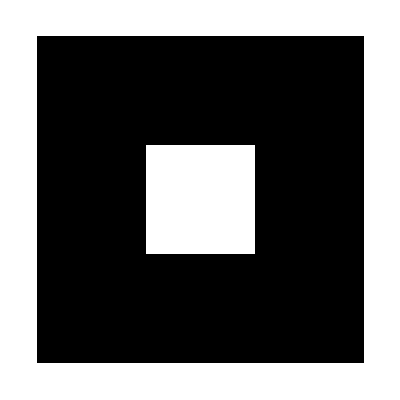
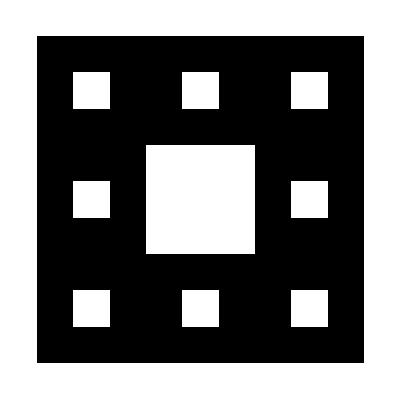
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot/@NestList[ArrayFlatten[{{#,#,#},{#,0,#},{#,#,#}}]&,{{1}},4]
```

```mathematica
Flatten[Table[If[IntegerQ[Sqrt[x^2+y^2]],{x,y,Sqrt[x^2+y^2]},Nothing],{x,20},{y,20}],1]
```

{{3,4,5},{4,3,5},{5,12,13},{6,8,10},{8,6,10},{8,15,17},{9,12,15},{12,5,13},{12,9,15},{12,16,20},{15,8,17},{15,20,25},{16,12,20},{20,15,25}}

```mathematica
Cases[Flatten[Table[If[IntegerQ[Sqrt[x^2+y^2]],{x,y,Sqrt[x^2+y^2]},Nothing],{x,20},{y,20}],1],{_,_,_}]
```

{{3,4,5},{4,3,5},{5,12,13},{6,8,10},{8,6,10},{8,15,17},{9,12,15},{12,5,13},{12,9,15},{12,16,20},{15,8,17},{15,20,25},{16,12,20},{20,15,25}}

```mathematica
(*Ahora convirtamoslos en numeros por que si*)
Total[{#[[1]]*100,#[[2]]*10,#[[3]] }]&/@{{3,4,5},{4,3,5},{5,12,13},{6,8,10},{8,6,10},{8,15,17},{9,12,15},{12,5,13},{12,9,15},{12,16,20},{15,8,17},{15,20,25},{16,12,20},{20,15,25}}
```

{345,435,633,690,870,967,1035,1263,1305,1380,1597,1725,1740,2175}

```mathematica
(*Ordenar 50 palabras random del espa;ol segun su ultima letra*)
```

```mathematica
SortBy[RandomChoice[WordList[Language->"Spanish"],50],Characters[#&][[-1]]]
```

{altanero,anisar,aposento,ausonio,ballestada,barrueco,boloñesa,cabedera,caneláceo,cascatreguas,catana,comendamiento,conterránea,coralito,cremación,cuartelero,cutidero,desmejorar,dimisionaria,enrafar,equilibrada,estofo,fez,flagrante,foraida,frívolamente,ganosa,gluten,hechura,imaginariamente,inexhausto,lanífera,llanca,macear,melenudo,mercado,mindanguear,mote,ovalar,peguera,pestilenciosa,prognato,reportamiento,riberano,rizal,sacadura,tambobón,tintillo,tronar,ungu¨ento}

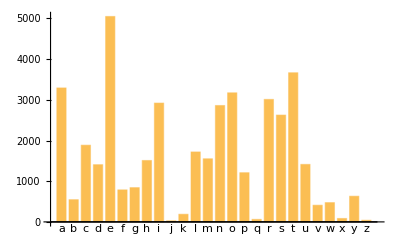

```mathematica
BarChart[KeyTake[LetterCounts[WikipediaData["computers"]],Alphabet[]],ChartLabels->Automatic]
```

```mathematica
(*/. es aplicar una regla a elementos de una lista*)
```

```mathematica
Clear[x,y]
{x,x,x,y,x}/.{x->1,y->2}
```

{1,1,1,2,1}

```mathematica
{x,x,x,x}/.x->RandomReal[]
```

{0.409701,0.409701,0.409701,0.409701}

```mathematica
{x,x,x,x}/.x->RandomReal[]
```

{0.732599,0.732599,0.732599,0.732599}

```mathematica
pdigitback[n_Integer /; n>0]:=Framed[Reverse[IntegerDigits[n]]]
```

```mathematica
pdigitback[2]
```

{2}

```mathematica
check[x_,y_]:=Red/;x>y
```

```mathematica
check[x_,y_]:=Green/;y>x
```

```mathematica
check[1,2]
```

RGBColor[0, 1, 0]

```mathematica
check[2,1]
```

RGBColor[1, 0, 0]